```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]


pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

(* 
https://blog.wolfram.com/2011/12/15/mathematica-qa-series-converting-to-conventional-mathematical-typesetting/
*)

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 116 Kb

{Utilities`CleanSlate`,VariationalMethods`,System`,Global`}

```mathematica
Clear[q]
q = 
{ r[t] , θ[t] }
```

{r[t],θ[t]}

```mathematica
Clear[s]
s = 
{ r[t] Sin[θ[t]] , r[t] Cos[θ[t]] }
```

{Cos[θ[t]] r[t],r[t] Sin[θ[t]]}

```mathematica
D[s, t]
```

{Cos[θ[t]] r'[t]-r[t] Sin[θ[t]] θ'[t],Sin[θ[t]] r'[t]+Cos[θ[t]] r[t] θ'[t]}

```mathematica
D[s, t] . D[s, t]
```

(Sin[θ[t]] r'[t]+Cos[θ[t]] r[t] θ'[t])^2+(Cos[θ[t]] r'[t]-r[t] Sin[θ[t]] θ'[t])^2

```mathematica
D[s, t] . D[s, t]  // Expand
```

Cos[θ[t]]^2 r'[t]^2+Sin[θ[t]]^2 r'[t]^2+Cos[θ[t]]^2 r[t]^2 θ'[t]^2+r[t]^2 Sin[θ[t]]^2 θ'[t]^2

```mathematica
D[s, t] . D[s, t]  // Expand  // Simplify
```

r'[t]^2+r[t]^2 θ'[t]^2

```mathematica
Clear[T]
T = 
1/2 m ( D[s, t] . D[s, t]  // Expand  // Simplify  )
```

1/2 m (r'[t]^2+r[t]^2 θ'[t]^2)

```mathematica
Clear[V]
V = 
- m g r[t] Cos[θ[t]] + 1/2 k ( r[t] -l0 )^2
```

-g m Cos[θ[t]] r[t]+1/2 k (-l0+r[t])^2

```mathematica
Clear[ℒ]
ℒ = 
T - V  ;
ℒ // pdConv
```

g m r(t) cos(θ(t))-1/2 k (r(t)-l0)^2+1/2 m ((r(t))^2 ((∂θ(t))/(∂t))^2+((∂r(t))/(∂t))^2)

```mathematica
D[ D[ ℒ , D[q[[1]], t] ], t ] - D[ ℒ , q[[1]] ] 
D[ D[ ℒ , D[q[[2]], t] ], t ] - D[ ℒ , q[[2]] ]
```

-g m Cos[θ[t]]+k (-l0+r[t])-m r[t] θ'[t]^2+m r''[t]

g m r[t] Sin[θ[t]]+2 m r[t] r'[t] θ'[t]+m r[t]^2 θ''[t]

```mathematica
Table[
D[ D[ ℒ , D[q[[i]], t] ], t ] - D[ ℒ , q[[i]] ] == 0 , 
{ i , 1, 2 } ]  // TableForm
```

-g m Cos[θ[t]]+k (-l0+r[t])-m r[t] θ'[t]^2+m r''[t]==0
g m r[t] Sin[θ[t]]+2 m r[t] r'[t] θ'[t]+m r[t]^2 θ''[t]==0

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

k l0+g m Cos[θ[t]]+r[t] (-k+m θ'[t]^2)-m r''[t]==0
-m r[t] (g Sin[θ[t]]+2 r'[t] θ'[t]+r[t] θ''[t])==0

```mathematica
Clear[parameters]
parameters = { 
m-> 1 , 
g-> 9.8 , 
l0-> 1 ,
k-> 20
};
parameters // TableForm
```

m→1
g→9.8
l0→1
k→20

```mathematica
eqs /. parameters // Expand // TableForm
```

20+9.8 Cos[θ[t]]-20 r[t]+r[t] θ'[t]^2-r''[t]==0
-9.8 r[t] Sin[θ[t]]-2 r[t] r'[t] θ'[t]-r[t]^2 θ''[t]==0

```mathematica
Clear[ics]
ics = {
r[0] == 1.1 ,
r'[0] == 0 ,
θ[0] == π/12 ,
θ'[0] == 0 
};
ics // TableForm
```

r[0]==1.1
r'[0]==0
θ[0]==π/12
θ'[0]==0

```mathematica
Clear[solution]
solution = 
First[NDSolve[ Union[ eqs /. parameters , ics ] , q , { t , 0 , 10 } ] ]
```

{r[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}

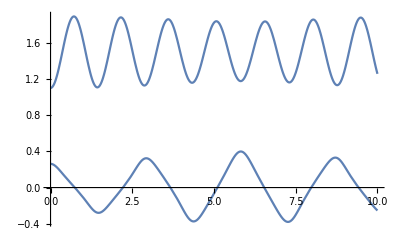

```mathematica
Plot[ q /. solution , { t, 0, 10 } ]
```

```mathematica
Clear[rReplace]
rReplace = 
Flatten[Solve[ λ[t]== ((r[t]-r0)/r0) , r[t] ] ]
```

{r[t]→r0 (1+λ[t])}

```mathematica
D[rReplace, t]
```

{r'[t]→r0 λ'[t]}

```mathematica
D[D[rReplace, t], t]
```

{r''[t]→r0 λ''[t]}

```mathematica
Clear[kgReplace]
kgReplace = {
k-> m Subscript[ω, 𝓈]^2 , (* use [esc]scs[esc] for script s, regular s defined above *) 
g-> r0 Subscript[ω, p]^2
};
kgReplace // TableForm
```

k→m ω_𝓈^2
g→r0 ω_p^2

```mathematica
Clear[λeqs]
λeqs = 
eqs  //. rReplace //. D[rReplace, t]  //. D[D[rReplace, t], t]   //. kgReplace // Expand // FullSimplify   ;
λeqs // TableForm
```

m (r0 Cos[θ[t]] ω_p^2+ω_𝓈^2 (l0-r0-r0 λ[t])+r0 (1+λ[t]) θ'[t]^2-r0 λ''[t])==0
m r0 (1+λ[t]) (Sin[θ[t]] ω_p^2+2 θ'[t] λ'[t]+(1+λ[t]) θ''[t])==0

```mathematica
Series[ λeqs , { θ[t] , 0 , 1 } ] // Normal // Expand  // Simplify 
(* Figure out how to drop higher order terms *)
```

{m (r0 ω_p^2+ω_𝓈^2 (l0-r0-r0 λ[t])+r0 (1+λ[t]) θ'[t]^2-r0 λ''[t])==0,m r0 (1+λ[t]) (ω_p^2 θ[t]+2 θ'[t] λ'[t]+(1+λ[t]) θ''[t])==0}